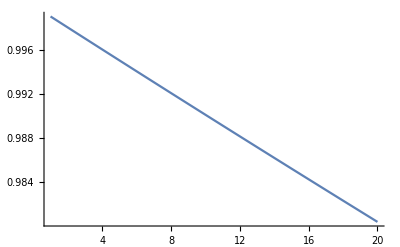

```mathematica
r=0.1;
k=1000;
b=1;
n[0]=1;
time=20; 
n[t_]:=n[t-1]/((1+n[t-1]/k)^b);
yy=Table[{n[t]},{t,1,time}]//Flatten;
xx=Range[time];
data=Transpose@{xx,yy};
ListLinePlot[data,PlotRange->Full]
```